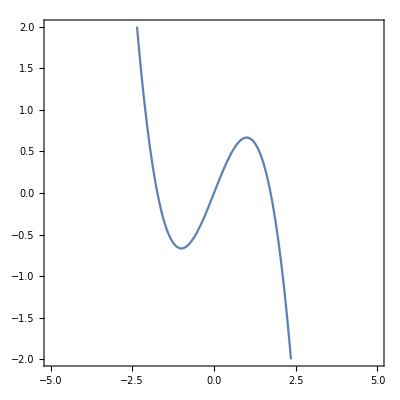

```mathematica
ContourPlot[v-v^3/3==w,{v,-5,5},{w,-2,2}]
```

```mathematica
Manipulate[Plot[v-v^3/3-kk,{v,-5,5}],{kk,-10,10}]
```

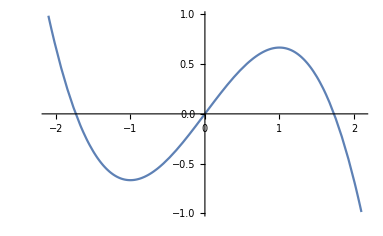

```mathematica
Plot[v-v^3/3,{v,-2.1,2.1}]
```

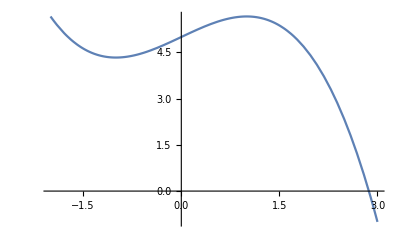

```mathematica
Plot[v-v^3/3+5,{v,-2,3},PlotRange->All]
```

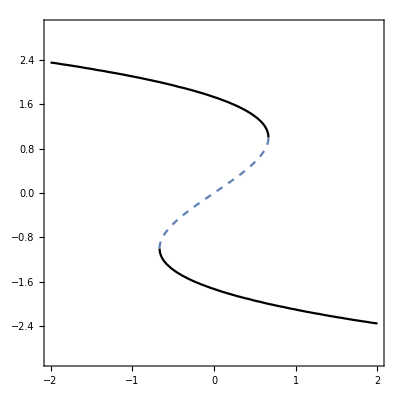

```mathematica
Show[ContourPlot[v-v^3/3==A,{A,-2,2},{v,-5,-1},ContourStyle->Black,PlotRange->{{-2,2},{-3,3}}],
ContourPlot[v-v^3/3==A,{A,-2,2},{v,-1,1},ContourStyle->Dashed,PlotRange->{{-2,2},{-3,3}}],
ContourPlot[v-v^3/3==A,{A,-2,2},{v,1,5},ContourStyle->Black,PlotRange->{{-2,2},{-3,3}}]]
```

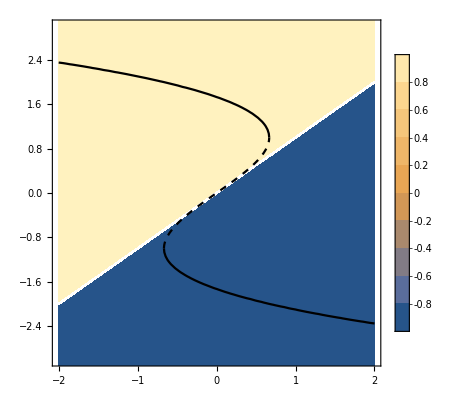

```mathematica
Show[ContourPlot[Sign[v-w],{w,-2,2},{v,-5,5},PlotRange->{{-2,2},{-3,3}},PlotLegends->Automatic],ContourPlot[v-v^3/3==w,{w,-2,2},{v,-5,-1},ContourStyle->Black,PlotRange->{{-2,2},{-3,3}},GridLines->{{0},{0}},AxesLabel->Automatic],
ContourPlot[v-v^3/3==w,{w,-2,2},{v,-1,1},ContourStyle->{Black,Dashed},PlotRange->{{-2,2},{-3,3}}],
ContourPlot[v-v^3/3==w,{w,-2,2},{v,1,5},ContourStyle->Black,PlotRange->{{-2,2},{-3,3}}]]
```

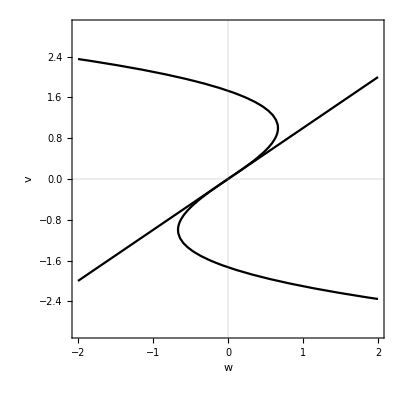

```mathematica
Show[ContourPlot[{v-v^3/3==w,v==w},{w,-2,2},{v,-5,5},ContourStyle->Black,PlotRange->{{-2,2},{-3,3}},GridLines->{{0},{0}},AxesLabel->Automatic,PlotLegends->Automatic]]
```